```mathematica
c=x(1-x)*y(1-y)
```

(1-x) x (1-y) y

```mathematica
u=2*(1-x)^2*x^2*(1-y)^2*y-2*(1-x)^2*x^2*(1-y)*y^2
```

2 (1-x)^2 x^2 (1-y)^2 y-2 (1-x)^2 x^2 (1-y) y^2

```mathematica
v=-2*(1-x)^2*x*(1-y)^2*y^2+2*(1-x)*x^2*(1-y)^2*y^2
```

-2 (1-x)^2 x (1-y)^2 y^2+2 (1-x) x^2 (1-y)^2 y^2

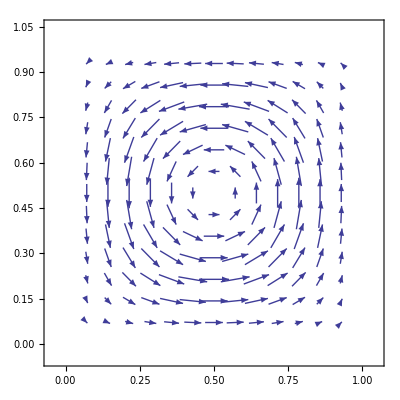

```mathematica
VectorPlot[{u,v},{x,0,1},{y,0,1}]
```

```mathematica
Clear[eps]
```

```mathematica
eps=10^(-5)
```

1/100000

```mathematica
Simplify[-eps (D[c,{x,2}]+D[c,{y,2}])+{u,v}.{D[c,x],D[c,y]}]
```

2 eps (x-x^2+y-y^2)

```mathematica
Simplify[{u,v}.{D[c,x],D[c,y]}]
```

0

```mathematica
Expand[-(D[c,{x,2}]+D[c,{y,2}])]
```

2 x-2 x^2+2 y-2 y^2